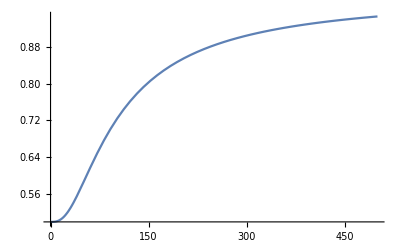

```mathematica
e1=(b/(Subscript[y, 1][s]+Subscript[y, 3][s]))*(Subscript[y, 1][s]*Subscript[y, 2][s]*Subscript[r, 1]+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*Subscript[r, 1]+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*Subscript[r, 2])-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 1][s];
e2=(b/(Subscript[y, 1][s]+Subscript[y, 3][s]))*(Subscript[y, 1][s]*Subscript[y, 2][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*(1-Subscript[r, 2]))-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 2][s];
e3=(b/(Subscript[y, 1][s]+Subscript[y, 3][s]))*(Subscript[y, 3][s]*Subscript[y, 4][s]*Subscript[r, 2]+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*Subscript[r, 1]+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*Subscript[r, 2])-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 3][s];
e4=(b/(Subscript[y, 1][s]+Subscript[y, 3][s]))*(Subscript[y, 3][s]*Subscript[y, 4][s]*(1-Subscript[r, 2])+(1/2)*Subscript[y, 2][s]*Subscript[y, 3][s]*(1-Subscript[r, 1])+(1/2)*Subscript[y, 1][s]*Subscript[y, 4][s]*(1-Subscript[r, 2]))-μ*(Subscript[y, 1][s]+Subscript[y, 2][s]+Subscript[y, 3][s]+Subscript[y, 4][s])*Subscript[y, 4][s];

(*FullSimplify[Solve[{e1==0,e2==0,e3==0,e4==0},{Subscript[y, 1][s],Subscript[y, 2][s],Subscript[y, 3][s],Subscript[y, 4][s]}]]*)

Subscript[r, 1] = 0.5;
Subscript[r, 2] = 0.1;
μ = 0.5;
b = 0.1;

sol:= NDSolve[{Subscript[y, 1]'[s] == e1,Subscript[y, 2]'[s] == e2,Subscript[y, 3]'[s] == e3,Subscript[y, 4]'[s] == e4,Subscript[y, 1][0] == 0.1,Subscript[y, 2][0]== 0.1,Subscript[y, 3][0] == 0.1,Subscript[y, 4][0] == 0.1},{Subscript[y, 1],Subscript[y, 2],Subscript[y, 3],Subscript[y, 4]},{s,0,1000}]


g4 =sol[[1]][[4]][[2]];
g3 = sol[[1]][[3]][[2]];
g2 = sol[[1]][[2]][[2]];
g1 = sol[[1]][[1]][[2]];

Prop = (Evaluate[g1[s]]+Evaluate[g2[s]])/(Evaluate[g1[s]]+Evaluate[g2[s]] + Evaluate[g3[s]]+Evaluate[g4[s]]);

Plot[Prop,{s,0,500}]

(*Plot[(g3+g4)/(g1+g2+g3+g4),{s,0,1000}]*)
```